## DeleteCell-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51 (05 June 2017)) loaded Wed 7 Jun 2017 10:45:07
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

Create a tissue with a point and an edge that aren't used.

There are 14 cells in the tissue.

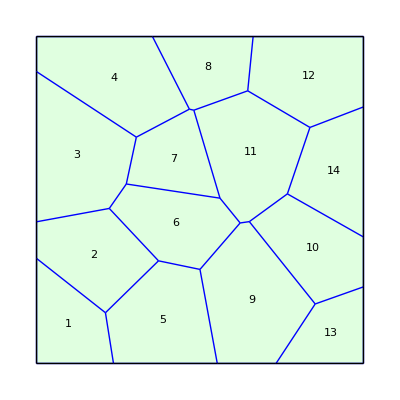

```mathematica
q=TemplateRandomSquareGrid[14, {-50, -50}, {50, 50}];
Q=Tissue2DTissue[q]; 
Print["There are ", NTissueCells[Q], " cells in the tissue."];  
ShowTissue[Q, "CellNumbers"-> True, Frame-> False, "EdgeStyles"-> Directive[Blue,Thick]]
```

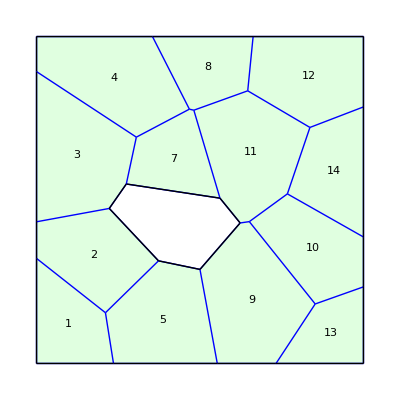

```mathematica
R=DeleteCell[Q,6];
ShowTissue[R, "CellNumbers"-> True, "EdgeStyles"-> Directive[Blue,Thick]]
```

```mathematica
Q
```

DTissue[{{-28.9206,-34.4819},{-27.7479,-2.58166},{-22.5414,4.89702},{-19.4702,19.2279},{-12.6938,-18.6058},{-3.24807,27.7846},{-1.88551,27.4677},{-0.00804308,-21.23},{6.11044,0.562264},{12.2769,-7.02411},{14.5996,33.3987},{15.0877,-6.61631},{26.7285,1.87287},{33.6251,22.1949},{35.2368,-31.799},{50,-50},{50,50},{-50,50},{-50,-50},{50.,-26.5656},{50.,-11.3149},{50.,28.4747},{16.247,50.},{-14.5387,50.},{-50.,39.2725},{-50.,-6.66312},{-50.,-17.8644},{-26.4619,-50.},{5.28591,-50.},{23.2577,-50.}},{{1,5},{1,27},{1,28},{2,3},{2,5},{2,26},{3,4},{3,9},{4,6},{4,25},{5,8},{6,7},{6,24},{7,9},{7,11},{8,10},{8,29},{9,10},{10,12},{11,14},{11,23},{12,13},{12,15},{13,14},{13,21},{14,22},{15,20},{15,30},{16,20},{16,30},{17,22},{17,23},{18,24},{18,25},{19,27},{19,28},{20,21},{21,22},{23,24},{25,26},{26,27},{28,29},{29,30}},{1→{36,3,2,35},2→{41,2,1,5,6},3→{40,6,4,7,10},4→{34,10,9,13,33},5→{42,17,11,1,3},6→{4,5,11,16,18,8},7→{7,8,14,12,9},8→{39,13,12,15,21},9→{43,28,23,19,16,17},10→{37,25,22,23,27},11→{14,18,19,22,24,20,15},12→{32,21,20,26,31},13→{27,28,30,29},14→{38,26,24,25}}]

```mathematica
R
```

DTissue[{{-28.9206,-34.4819},{-27.7479,-2.58166},{-22.5414,4.89702},{-19.4702,19.2279},{-12.6938,-18.6058},{-3.24807,27.7846},{-1.88551,27.4677},{-0.00804308,-21.23},{6.11044,0.562264},{12.2769,-7.02411},{14.5996,33.3987},{15.0877,-6.61631},{26.7285,1.87287},{33.6251,22.1949},{35.2368,-31.799},{50,-50},{50,50},{-50,50},{-50,-50},{50.,-26.5656},{50.,-11.3149},{50.,28.4747},{16.247,50.},{-14.5387,50.},{-50.,39.2725},{-50.,-6.66312},{-50.,-17.8644},{-26.4619,-50.},{5.28591,-50.},{23.2577,-50.}},{{1,5},{1,27},{1,28},{2,3},{2,5},{2,26},{3,4},{3,9},{4,6},{4,25},{5,8},{6,7},{6,24},{7,9},{7,11},{8,10},{8,29},{9,10},{10,12},{11,14},{11,23},{12,13},{12,15},{13,14},{13,21},{14,22},{15,20},{15,30},{16,20},{16,30},{17,22},{17,23},{18,24},{18,25},{19,27},{19,28},{20,21},{21,22},{23,24},{25,26},{26,27},{28,29},{29,30}},{1→{36,3,2,35},2→{41,2,1,5,6},3→{40,6,4,7,10},4→{34,10,9,13,33},5→{42,17,11,1,3},7→{7,8,14,12,9},8→{39,13,12,15,21},9→{43,28,23,19,16,17},10→{37,25,22,23,27},11→{14,18,19,22,24,20,15},12→{32,21,20,26,31},13→{27,28,30,29},14→{38,26,24,25}}]

```mathematica
TissueCells[R]
```

{1→{36,3,2,35},2→{41,2,1,5,6},3→{40,6,4,7,10},4→{34,10,9,13,33},5→{42,17,11,1,3},7→{7,8,14,12,9},8→{39,13,12,15,21},9→{43,28,23,19,16,17},10→{37,25,22,23,27},11→{14,18,19,22,24,20,15},12→{32,21,20,26,31},13→{27,28,30,29},14→{38,26,24,25}}